## Predator-Prey Ecosystem: A Real-Time Agent-Based Simulation

## Initialisation Parameters

```mathematica
(* Enum for agent types *)
Shark=1.;
Sardine=2.;
Algae = 3.;
Trawler = 4.;

(* Size of initial population of Algae & algae endurance *)
initialAlgae = 100.;
algaeEndurance = 20;

sharkSight = 0.25;
sardineSight = 0.15;

(* Cap population members*)
maxSardines=500.;
maxSharks=500.;
maxAlgae = 1500.;

dummyPoint={-1.,-1.};

(* Seed random for reproducability *)
SeedRandom["A trout is a moment of beauty known only to those who seek it - fisherman's saying"]

(* VECTOR GEOMETRY HELPER FUNCTIONS FOR EASY MODIFICATION *)

getTrawlerRect[centroid_, tSize_]:=
(* Helper function returns rectangle around specified centroid *)
Rectangle[ 
{centroid[[1]] - (0.1 * tSize ) , centroid[[2]] - (0.1 * tSize )},
 {centroid[[1]] + (0.1 * tSize ) , centroid[[2]] + (0.1 * tSize )}]

trawlerCollision[point_, trawler_, tSize_]:=
(* return weather point contained in trawler. 
- Faster than wolfram built-in collision function 
  - Assumes circular trawlers for speed*)
(Norm[ point - trawler[[{1, 2}]] ] <0.1 * tSize )

FromPolar[r_, theta_]:= 
{r Cos[theta], r Sin[theta]}

(* Oof *)
ToPolar[xy_]:=
If[xy[[1]] == 0.&& xy[[2]]== 0.,
ToPolarCoordinates[{xy[[1]]+0.001, xy[[2]]+0.001}],
ToPolarCoordinates[xy]
]
```

RandomGeneratorState[…]

```mathematica
CheckAbort[ArcTan[0, 0],False] == False
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

Indeterminate==False

## Construct Initial Populations

```mathematica
initialAgents[]:=
Join[
Table[ (* Proportion of fish population made up of guppies and sharks *)
Join[
RandomReal[{0,1},2],(* Location *)
{0.,If[RandomReal[]<0.1,Shark,Sardine]}
]
,{100}
],
(* Initial population of Algae *)
Table[
Join[
RandomReal[{0,1},2],(* Location *)
{0.,Algae}]
, {initialAlgae}
]
]
```

## Display Environment

```mathematica
visualizeEnvironment[agents_, prettyPrint_, tSize_]:=Module[
{
sharks=Take[#,2]&/@Select[agents,(#[[4]]==Shark)&],
sardines=Take[#,2]&/@Select[agents,(#[[4]]==Sardine)&],
algae=Take[#,2]&/@Select[agents,(#[[4]]==Algae)&],
trawlers = Take[#,3]&/@Select[agents,(#[[4]]==Trawler)&],
duddTrawlers = Take[#,2]&/@Select[agents,(#[[4]]==Trawler)&],
dummyList={dummyPoint}
},
Show[
(* Draw Algae *)
Graphics[{
AbsolutePointSize[5],RGBColor[.11,.60,.11],
Point@If[algae=={},dummyList,algae]
}],

(* Draw Sardines *)
If[prettyPrint,
Graphics[(Style[Text["🐠", #],RGBColor[.0,.25,.5], Bold, FontFamily->"Arial"])&/@If[sardines=={},dummyList,sardines]],
Graphics[{
AbsolutePointSize[10],RGBColor[.0,.25,.5],
Point@If[sardines=={},dummyList,sardines]
}]
],

(* Draw Sharks *)
If[prettyPrint,
Graphics[Triangle[{#, #+{0.015, 0}, # + {0.02 ,0.02}}]&/@If[sharks=={},dummyList,sharks]],
Graphics[{
AbsolutePointSize[15],RGBColor[.0,.1,.3],
Point@If[sharks=={},dummyList,sharks]
}]
],

(* Draw Trawlers *) 
Graphics[({Opacity[0.2],  Pink , EdgeForm[Dashed], getTrawlerRect[ #[[{1, 2}]], tSize]})&/@If[trawlers=={},{{-1, -1, 0}},trawlers]],

(* Display Trawler Centroids
Graphics[{
AbsolutePointSize[30],RGBColor[.9,.25,.5],
Point@If[  duddTrawlers== {}, dummyList,duddTrawlers]
}],
*)

ImageSize->{600,600},
AspectRatio->Automatic,
Frame->False,
Axes->False,
PlotRange->{{0.,1.},{0.,1.}}
]
]
```

## Agent Behaviour

```mathematica
(* Trawler Behaviour *)
updateTrawler[trawler_, tSpeed_]:=
(* Delete Trawler when out of bounds *)
If[Norm[trawler[[{1,2}]] - {0.5, 0.5}] < 1,
(* Move trawler at constant speed in desired direction *)
{Join[ 
trawler[[{1,2}]] + {tSpeed * Cos[trawler[[3]]], tSpeed * Sin[trawler[[3]]]}
, {trawler[[3]], Trawler}
]},
{}
]

newTrawler[]:= Module[ {origin, terminus},
Switch[
RandomInteger[{1, 4}],
(* L -> R *)
1,
origin = {0., RandomReal[{0., 1.}]};
terminus = {1., RandomReal[{0., 1.}]};
Join[origin, {ToPolar[terminus - origin][[2]], Trawler}],

(* R -> L *)
2,
origin = {1., RandomReal[{0., 1.}]};
terminus = {0., RandomReal[{0., 1.}]};
Join[origin, {ToPolar[terminus - origin][[2]], Trawler}],

(* T -> B *)
3,
origin = {RandomReal[{0., 1.}], 0.};
terminus = {RandomReal[{0., 1.}], 1.};
Join[origin, {ToPolar[terminus - origin][[2]], Trawler}],

(* B -> T *)
4,
origin = {RandomReal[{0., 1.}], 1.};
terminus = {RandomReal[{0., 1.}], 0.};
Join[origin, {ToPolar[terminus - origin][[2]], Trawler}]
]
]
```

## Update Population

```mathematica
updateAgents[agents_,
sardineGrowthRate_,
sardineMobility_,
sharkGrowthRate_,
sharkMobility_,
sharkEndurance_, 
sardineEndurance_,
algaeGrowthRate_,
tSize_,
tSpeed_,
tSpawnRate_,
smartSharks_,
smartSardines_,
targetAlgae_,
targetSardines_,
targetSharks_]:=Module[{
sharkPop=Length[Select[agents,(#[[4]]==Shark)&]],
algaePop = Length[Select[agents,(#[[4]]==Algae)&]],
sardinePop=Length[Select[agents,(#[[4]]==Sardine)&]],
nearestSharks=Nearest[Append[Take[#,2]&/@Select[agents,(#[[4]]==Shark)&],dummyPoint]],
nearestSardines=Nearest[Append[Take[#,2]&/@Select[agents,(#[[4]]==Sardine)&],dummyPoint]],
nearestAlgae = Nearest[Append[Take[#,2]&/@Select[agents,(#[[4]]==Sardine)&],dummyPoint]],
nearestTrawler = Nearest[Append[Take[#,2]&/@Select[agents,(#[[4]]==Trawler)&],dummyPoint]],
i,nextLocation, currentLocation, ag, survivors, data = {0,0,0} (* data = {fishBorn, fishCaught, fishDead} *)
},
ag = Join[
Table[

survivors={};

currentLocation = agents[[i, {1,2}]];
nextLocation =agents[[i,{1,2}]]+ 
If[agents[[i, 4]] == Sardine,
(*
FromPolar[RandomReal[{0, sardineMobility}], RandomReal[{0, 1}] * 2Pi ],*)
If[! smartSardines ||  nearestSharks[currentLocation][[1]] == dummyPoint || Norm[nearestSharks[currentLocation][[1]] - currentLocation] > sardineSight,

FromPolar[RandomReal[{0, sardineMobility}], RandomReal[{0, 1}] * 2Pi ],
FromPolar[RandomReal[{0,sardineMobility}], ToPolar[ nearestSharks[currentLocation][[1]]- currentLocation][[2]] + Pi]

],
If[
(* If smart sharks arent enabled or the nearest fish is the dummy point, move randomly *)
(! smartSharks|| nearestSardines[currentLocation][[1]] == dummyPoint || Norm[nearestSardines[currentLocation][[1]] - currentLocation] > sharkSight),
FromPolar[RandomReal[{0, sharkMobility}], RandomReal[{0, 1}] * 2Pi ],
FromPolar[RandomReal[{0, sharkMobility}], ToPolar[ nearestSardines[currentLocation][[1]]- currentLocation][[2]]]
]
];
(*
If[agents[[i,4]]==Sardine,
RandomReal[{-sardineMobility,sardineMobility},2],
RandomReal[{-sharkMobility,sharkMobility},2]
];
*)

nextLocation=Clip[nextLocation,{0.,1.}];

Switch[
(* Implement each agents behaviour based on type *)
agents[[i, 4]],

(* sardines' behavior *)
Sardine,


If[Norm[nearestSharks[nextLocation][[1]]-nextLocation]>0.02 
&& agents[[i,3]]<sardineEndurance,
(* If not eaten by Shark or starved*)
If[!( RandomReal[] >targetSardines && trawlerCollision[nextLocation, nearestTrawler[nextLocation][[1]], tSize]),
(* Fish is not caught by trawler *)
(* Update hunger depending wether or not it ate *)
survivors = If[ Norm[nearestAlgae[nextLocation][[1]]-nextLocation]>0.02,
{Join[nextLocation,{agents[[i,3]]+1.,Sardine}]},
{Join[nextLocation,{0.,Sardine}]}
];
(* Probabilistic reproduction with logistic growth restriction; adding one more sardine *)
If[RandomReal[]<sardineGrowthRate(1.-sardinePop/maxSardines),
AppendTo[survivors,Join[nextLocation,{0.,Sardine}]];
data[[1]] = data[[1]]+1 (* add newbord fish to stats *)
],
(* Fish was caught by trawler *)
data[[2]] = data[[2]]+1 
],

(* If eaten by a shark or starved *)
data[[3]] = data[[3]] + 1
],

(* sharks' behavior *)
Shark,
If[!( RandomReal[] > targetSharks && trawlerCollision[nextLocation, nearestTrawler[nextLocation][[1]], tSize]),
If[
Norm[nearestSardines[nextLocation][[1]]-nextLocation]>0.02,

If[agents[[i,3]]<sharkEndurance,
(* starving but still survive *)
survivors={Join[nextLocation,{agents[[i,3]]+1.,Shark}]};
],

(* just ate sardine and survive *)
survivors={Join[nextLocation,{0.,Shark}]};
If[RandomReal[]<sharkGrowthRate(1.-sharkPop/maxSharks),
AppendTo[survivors,Join[nextLocation,{0.,Shark}]]
](* Probabilistic reproduction; adding one more shark *)
]
],

(* Algae behaviour *)
Algae,
If[ Norm[nearestSardines[currentLocation][[1]]-currentLocation]>0.02
&& !(  RandomReal[] >targetAlgae && trawlerCollision[currentLocation, nearestTrawler[currentLocation][[1]], tSize])
&& agents[[i,3]]<algaeEndurance,

survivors={Join[agents[[i,{1,2}]],{agents[[i,3]] + 1,Algae}]}];



(* TODO: Algae reproduction decouppled from parents *)
If[RandomReal[]<algaeGrowthRate(1.-algaePop/maxAlgae),
AppendTo[survivors,Join[ RandomReal[{0, 1}, 2],{0. ,Algae}]]
],

(* Trawler Behaviour *)
Trawler,
survivors = updateTrawler[agents[[i]], tSpeed]

];

survivors

,{i,Length[agents]}

]//Flatten[#,1]&,

(* Spawn new trawler, independent of current population *)

If[RandomInteger[{0, tSpawnRate}] == 1,
{newTrawler[]},
{}]


]//Developer`ToPackedArray;
Return[{ag, data}]
]
```

## Plot Constructors for Species Population

```mathematica
constructIndividualPopulationPlots[populations_]:=
(* Helper function that takes List of {{Algae}, {Sardines}, {Sharks}} for each step of simulation so far *)
GraphicsColumn[
{
(* Evaluate inb4 to improve performance*)
ListLinePlot[
populations[[1]]
,PlotLabel-> "Algae Population Over Time"
,PlotStyle -> RGBColor[.11,.60,.11]
,AxesLabel -> {"Time (No. Iterations)", "No. Individuals"}
, Filling->Axis],

ListLinePlot[
populations[[2]]
,PlotLabel-> "Sardine Population Over Time"
,PlotStyle->RGBColor[.0,.25,.5]
,AxesLabel -> {"Time (No. Iterations)", "No. Individuals"}
, Filling->Axis],

ListLinePlot[
populations[[3]]
,PlotLabel-> "Shark Population Over Time"
,PlotStyle->RGBColor[.0,.1,.5]
,AxesLabel -> {"Time (No. Iterations)", "No. Individuals"}
, Filling->Axis]
}
]

constructCompositePopulationPlot[populations_] := 
ListLinePlot[
populations, 
PlotLegends->{"Algae","Sardines","Sharks"}, 
PlotLabel -> "Species Population Over Time",  
AxesLabel -> {"Time (No. Iterations)", "No. Individuals"},
PlotStyle->{RGBColor[.11,.60,.11], RGBColor[.0,.25,.5], RGBColor[.0,.1,.3]}
, Filling->Axis]



constructIndividualDeathPlots[populations_]:=
(* Helper function that takes List of {{Algae}, {Sardines}, {Sharks}} for each step of simulation so far *)
GraphicsColumn[
{
(* Evaluate inb4 to improve performance*)
ListLinePlot[
populations[[1]]
,PlotLabel-> "Total Sardines Born Over Time"
,PlotStyle -> RGBColor[.6,.6,.0]
,AxesLabel -> {"Time (No. Iterations)", "No. Individuals"}
, Filling->Axis],

ListLinePlot[
populations[[2]]
,PlotLabel-> "Total Sardines Caught Over Time"
,PlotStyle->RGBColor[.6,.3,.3]
,AxesLabel -> {"Time (No. Iterations)", "No. Individuals"}
, Filling->Axis],

ListLinePlot[
populations[[3]]
,PlotLabel-> "Total Sardine Deaths by Natural Causes Over Time"
,PlotStyle->RGBColor[.0,.0,.0]
,AxesLabel -> {"Time (No. Iterations)", "No. Individuals"}
, Filling->Axis]
}
]

constructCompositeDeathPlot[populations_] := 
ListLinePlot[
populations, 
PlotLegends->{"Births","Caught","Deaths"}, 
PlotLabel -> "Sardine Population Dynamics Over Time",  
AxesLabel -> {"Time (No. Iterations)", "No. Individuals"},
PlotStyle->{RGBColor[.6,.6,.0], RGBColor[.6,.3,.3], RGBColor[.0,.0,.0]}
, Filling->Axis]
```

## Display Interactive Simulation

```mathematica
Manipulate[
Refresh[
(* Update population *)
If[moving,
  res=updateAgents[ag,sardineGrowthRate,sardineMobility,sharkGrowthRate,sharkMobility,sharkEndurance, sardineEndurance, algaeGrowthRate, tSize,tSpeed, 50 - tSpawnRate,smartSharks, smartSardines,targetAlgae, targetSardines, targetSharks];  
ag = res[[1]]; (* Store updated populations for plot *)
pd = res[[2]];
AppendTo[pop[[1]], Length[Select[ag,(#[[4]]==Algae)&]]];
AppendTo[pop[[2]], Length[Select[ag,(#[[4]]==Sardine)&]]];
AppendTo[pop[[3]], Length[Select[ag,(#[[4]]==Shark)&]]];

AppendTo[popDyn[[1]],pd[[1]]];
AppendTo[popDyn[[2]],pd[[2]]];
AppendTo[popDyn[[3]],pd[[3]]]
];
visualizeEnvironment[ag, prettyPrint, tSize]
,UpdateInterval->If[moving,0,Infinity]
]
,""
,Style["Simulation Settings:", 16]
,Grid[
{
{
Style["ALGAE PROPERTIES", Bold]
,Style["SARDINE PROPERTIES", Bold]
,Style["SHARK PROPERTIES",Bold]
,Style["TRAWLER PROPERTIES", Bold]
}
,{
Control[{{algaeGrowthRate,0.5,"growth rate"},0,1,ImageSize->Tiny}]
,Control[{{sardineGrowthRate,0.5,"growth rate"},0,1,ImageSize->Tiny}]
,Control[{{sharkGrowthRate,0.5,"growth rate"},0,1,ImageSize->Tiny}]
, Control[{{tSpawnRate, 45, "spawn rate"}, 0, 50,1, ImageSize -> Tiny}]
}
,{
" "
,Control[{{sardineMobility,0.06,"mobility"},0,0.1,ImageSize->Tiny}]
,Control[{{sharkMobility,0.1,"mobility"},0,0.1,ImageSize->Tiny}]
, Control[{{tSpeed, 0.1, "speed"}, 0, 0.5, ImageSize -> Tiny}]
}
,{
" "
,Control[{{sardineEndurance,10,"starvation"},1,20,1,Appearance->"Labeled",ImageSize->Tiny}]
,Control[{{sharkEndurance,10,"starvation"},1,20,1,Appearance->"Labeled",ImageSize->Tiny}]
, Control[{{tSize, 1, "size"}, 0, 2.5, ImageSize -> Tiny}]
}
},
Frame->{{1,2,3}-> True,1->True}
,Alignment->Center]
," "
, Style["TRAWLER TARGET SPECIES", Bold]
,Grid[
{
{
Control[{{targetAlgae,0.99,"Algae Throwback"},0,1,ImageSize->Tiny}],
Control[{{targetSardines,0.01,"Sardine Throwback"},0,1,ImageSize->Tiny}],
Control[{{targetSharks,0.5,"Shark Throwback"},0,1,ImageSize->Tiny}]
}
},Frame-> All]
," "
,{{ag,initialAgents[]},ControlType->None}
,{{res, {{{-1, -1, 0, 1.}}, {}}}, ControlType->None}
(* Population proportions *)
,{{pop,{{0}, {0}, {0}}}, ControlType->None}
(* Target species population change proportions *)
,{{popDyn, {{0}, {0}, {0}}}, ControlType -> None}
,{{fname, "save.dat"}, ControlType->None}
," "
,Item[Grid[
{
{Control[{{moving,False,Style["RUN SIMULATION", Bold]},{True, False}}]},
{Control[{{prettyPrint,False,Style["PRETTY PRINTING", Bold]},{False,True}}]},
{Control[{{smartSharks,True,Style["EFFICIENT SHARKS", Bold]},{False,True}}]},
{Control[{{smartSardines,True,Style["EFFICIENT SARDINES", Bold]},{False,True}}]},
{Button["Reset",moving=False;ag=initialAgents[];res ={{{-1, -1, 0, 1.}},{}}; pop={{0},{0},{0}}; popDyn = {{0},{0},{0}},ImageSize->Medium]},
{Button["Save Sim",filePath=SystemDialogInput["FileSave"];Export[filePath, Join[{pop}, {popDyn}], "Package"], ImageSize->Medium, Method->"Queued"]
},
{Button["Step", res=updateAgents[ag,sardineGrowthRate,sardineMobility,sharkGrowthRate,sharkMobility,sharkEndurance, sardineEndurance, algaeGrowthRate, tSize,tSpeed, 50 - tSpawnRate,smartSharks, smartSardines,targetAlgae, targetSardines, targetSharks];
ag = res[[1]];
pd = res[[2]];
AppendTo[pop[[1]], Length[Select[ag,(#[[4]]==Algae)&]]];
AppendTo[pop[[2]], Length[Select[ag,(#[[4]]==Sardine)&]]];
AppendTo[pop[[3]], Length[Select[ag,(#[[4]]==Shark)&]]];
AppendTo[popDyn[[1]],pd[[1]]];
AppendTo[popDyn[[2]],pd[[2]]];
AppendTo[popDyn[[3]], pd[[3]]]
, ImageSize->Medium]}
}, Frame-> All], ControlPlacement->Right]
," "
,SaveDefinitions->True,AutorunSequencing->{6},TrackedSymbols:>{moving,ag},
SynchronousUpdating->True,ControlPlacement->Bottom
]
```

```mathematica
ArcTan[0.001,0.001]
```

0.785398

## DATA ANALYSIS & PLOTTING

```mathematica
Manipulate[
plots,
Grid[{
{" " 
,Button["Load Data",plotFile=SystemDialogInput["FileOpen"];res =  Import[plotFile, "Package"]; pop=res[[1]]; popDyn = res[[2]];  plots = constructIndividualPlots[pop],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Control[{{avgNo,10,"Moving average of:"},1,300,1,Appearance->"Labeled",ImageSize->Tiny}]
," "}
,{" "
,Button["Pop Size Individually",plots = constructIndividualPopulationPlots[pop],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Button["Pop Avg Individual", algae = MovingAverage[pop[[1]], avgNo]; sardines = MovingAverage[pop[[2]], avgNo]; sharks = MovingAverage[pop[[3]], avgNo];plots = constructIndividualPopulationPlots[{algae, sardines, sharks}],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Button["Pop size Composite",plots = constructCompositePopulationPlot[pop],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Button["Pop Avg Composite", algae = MovingAverage[pop[[1]], avgNo]; sardines = MovingAverage[pop[[2]], avgNo]; sharks = MovingAverage[pop[[3]], avgNo];plots = constructCompositePopulationPlot[{algae, sardines, sharks}],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Button["Deaths Individually",plots = constructIndividualDeathPlots[popDyn],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Button["Deaths Composite",plots = constructCompositeDeathPlot[popDyn],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Button["Death Avg Composite", births = MovingAverage[popDyn[[1]], avgNo]; caught = MovingAverage[popDyn[[2]], avgNo]; deaths = MovingAverage[popDyn[[3]], avgNo];plots = constructCompositeDeathPlot[{births, caught, deaths}],ImageSize->Large, Method->"Queued"]
," "}
,{" "
,Button["Save Figure",saveFile=SystemDialogInput["FileSave"]; Export[saveFile, plots, "SVG"],ImageSize->Large, Method->"Queued"] 
," "}
,{" "
,Button["Death Avg Composite", births = MovingAverage[popDyn[[1]], avgNo]; caught = MovingAverage[popDyn[[2]], avgNo]; deaths = MovingAverage[popDyn[[3]], avgNo];plots = constructIndividualDeathPlots[{births, caught, deaths}],ImageSize->Large, Method->"Queued"]
," "}

}, Frame-> All]
,ControlPlacement->Right
]
```

## TESTING HARNESS

```mathematica
runExperiment[params_, n_] :=Module[{i,ag, pd, pop={{0}, {0}, {0}}, popDyd={{0}, {0}, {0}}},
ag=initialAgents[]; 
For[i=0,i<n,i++,
res = updateAgents[ag,params["sardineGrowthRate"], params["sardineMobility"],params["sharkGrowthRate"],params["sharkMobility"],params["sharkEndurance"], params["sardineEndurance"], params["algaeGrowthRate"], params["tSize"],params["tSpeed"], params["tSpawnRate"],params["smartSharks"], params["smartSardines"], params["targetAlgae"], params["targetSardines"], params["targetSharks"]];
ag = res[[1]];
pd = res[[2]];

AppendTo[pop[[1]], Length[Select[ag,(#[[4]]==Algae)&]]];
AppendTo[pop[[2]], Length[Select[ag,(#[[4]]==Sardine)&]]];
AppendTo[pop[[3]], Length[Select[ag,(#[[4]]==Shark)&]]];

(*
AppendTo[popDyn[[1]],pd[[1]]];
AppendTo[popDyn[[2]],pd[[2]]];
AppendTo[popDyn[[3]],pd[[3]]];
*)
If[Length[Select[ag,(#[[4]]==Sardine)&]]==0||Length[Select[ag,(#[[4]]==Shark)&]]==0 || Length[Select[ag,(#[[4]]==Algae)&]]==0,
Break[]]
];
(*{pop, popDyn}*)
pop

]


runBatch[params_, numExp_, expLen_, verbose_] :=Module[
{batchRes = { {},{},{},{},{},{}}, i, pop},
(* Run numExp experiments of expLen steps at params_ parameters

Return: Dict of lists of length numExp meanign { 
{FinalAlg}, 
{FinalSard}, 
{FinalShark}, 
{AvgSard}, 
{AvgAlg}, 
{AvgShark}}
 *)
For[i = 1, i ≤ numExp, i++, 
pop = runExperiment[params, expLen];
If[verbose,
Print[i]];
(* Add experiment results to *)
AppendTo[batchRes[[1]], pop[[1, -1]] ];
AppendTo[batchRes[[2]], pop[[2, -1]] ];
AppendTo[batchRes[[3]], pop[[3, -1]] ];

AppendTo[batchRes[[4]], Mean[ pop[[1]] ] ];
AppendTo[batchRes[[5]],Mean[ pop[[2]] ] ];
AppendTo[batchRes[[6]], Mean[pop[[3]] ] ];
];

batchRes
]

checkStability[params_, numExp_, expLen_, verbose_]:= Module[{stable, total, results, i},
(* Returns percentage of runs for which populations remained stable -- no extinction *)
results = runBatch[params, numExp, expLen,verbose];
stable = 0;
total = Length[ results[[1]] ];
For[ i = 1, i ≤ total, i++,
If[ !(results[[1, i]] == 0 || results[[2, i]] == 0  || results[[3, i]] == 0 ),
stable += 1;
];
];
Return[stable / total]
]

(* Lazy implementation that copies code because it is getting late *)
runCascade[params_, n_, newTargetShark_] :=Module[{i,ag, pd, faze, res, stab = True, popOrig={{0}, {0}, {0}}, popExp = {{0}, {0}, {0}}, popDyd={{0}, {0}, {0}}},
ag=initialAgents[]; 
faze = Quotient[n, 2];

(* Run at parameters before exploitation *)
For[i=0,i<n,i++,
res = updateAgents[ag,params["sardineGrowthRate"], params["sardineMobility"],params["sharkGrowthRate"],params["sharkMobility"],params["sharkEndurance"], params["sardineEndurance"], params["algaeGrowthRate"], params["tSize"],params["tSpeed"], params["tSpawnRate"],params["smartSharks"], params["smartSardines"], params["targetAlgae"], params["targetSardines"], params["targetSharks"]];
ag = res[[1]];
AppendTo[popOrig[[1]], Length[Select[ag,(#[[4]]==Algae)&]]];
AppendTo[popOrig[[2]], Length[Select[ag,(#[[4]]==Sardine)&]]];
AppendTo[popOrig[[3]], Length[Select[ag,(#[[4]]==Shark)&]]];

If[Length[Select[ag,(#[[4]]==Sardine)&]]==0||Length[Select[ag,(#[[4]]==Shark)&]]==0 || Length[Select[ag,(#[[4]]==Algae)&]]==0,
stab = False;
Return[{{},{},{}, False}]
]
];
(* Introduce exploitation*)
For[i=0,i<n,i++,
res = updateAgents[ag,params["sardineGrowthRate"], params["sardineMobility"],params["sharkGrowthRate"],params["sharkMobility"],params["sharkEndurance"], params["sardineEndurance"], params["algaeGrowthRate"], params["tSize"],params["tSpeed"], params["tSpawnRate"],params["smartSharks"], params["smartSardines"], params["targetAlgae"], params["targetSardines"], newTargetShark];
ag = res[[1]];
AppendTo[popExp[[1]], Length[Select[ag,(#[[4]]==Algae)&]]];
AppendTo[popExp[[2]], Length[Select[ag,(#[[4]]==Sardine)&]]];
AppendTo[popExp[[3]], Length[Select[ag,(#[[4]]==Shark)&]]];

If[Length[Select[ag,(#[[4]]==Sardine)&]]==0||Length[Select[ag,(#[[4]]==Shark)&]]==0 || Length[Select[ag,(#[[4]]==Algae)&]]==0,
stab = False;
Break[]]
];

(*Return mean populations before and after introduction of exploitation *)
{
{Mean[popOrig[ [1]] ] ,Mean[popExp[[1]] ]},
{Mean[ popOrig[[2]] ] ,Mean[popExp[[2]] ]},
{ Mean[ popOrig[[3]] ],Mean[popExp[[3]] ]},
stab
}
]

runCascadeBatch[params_, numExp_, expLen_,newTargetShark_ , verbose_] :=Module[
{batchRes = {{{},{},{}},{{},{},{}}}, i, pop},
For[i = 1, i ≤ numExp, i++, 
pop = runCascade[params, expLen, newTargetShark];
If[verbose,
Print[i]];

AppendTo[batchRes[[1, 1]], pop[[1, 1]] ];
AppendTo[batchRes[[1, 2]], pop[[2, 1]] ];
AppendTo[batchRes[[1, 3]], pop[[3, 1]] ];

AppendTo[batchRes[[2, 1]],  pop[[1, 2]]  ];
AppendTo[batchRes[[2, 2]], pop[[2, 2]]  ];
AppendTo[batchRes[[2, 3]], pop[[3, 2]]  ];
];

batchRes
]


checkExploitationRange[params_, numExp_, expLen_, interval_, verbose_]:= Module[{},
(* Returns percentage of runs for which populations remained stable over a range of sardine exploitation rates *)
( params["targetSardines"] = #; Print[#]; checkStability[params, numExp, expLen, verbose]) & /@ Range[0, 1, interval]
]
```

### TESTING PARAMETERS TEMPLATE

```mathematica
(* Enum for agent types *)
Shark=1.;
Sardine=2.;
Algae = 3.;
Trawler = 4.;

(* Size of initial population of Algae & algae endurance *)
initialAlgae = 100.;
algaeEndurance = 20;

sharkSight = 0.25;
sardineSight = 0.15;

(* Cap population members*)
maxSardines=800.;
maxSharks=500.;
maxAlgae = 1500.;

dummyPoint={-1.,-1.};
```

```mathematica
(* Behavioural parameters *)
data["algaeGrowthRate"] =0.725;
data["sardineGrowthRate"]=0.455;
data["sharkGrowthRate"]=0.15;

data["sardineMobility"]=0.06;
data["sharkMobility"]=0.068;


data["sardineEndurance"] =10;
data["sharkEndurance"]=15;

(* Trawler settings *)
data["tSpawnRate"] = 5;
data["tSpeed"]=0.1;
data["tSize"]= 1;

data["targetAlgae"]=0.99;
data["targetSardines"]=0.99;
data["targetSharks"]=0.5;

(* Agent type *)
data["smartSharks"]= True;
data["smartSardines"] = True;



res ={{{-1, -1, 0, 1.}},{}};
pop={{0},{0},{0}};
popDyn = {{0},{0},{0}};
```

```mathematica
(* Time: CCa 3 Hours? runCascadeBatch[data,30,600,0.8,True] *)
```

## DATA ANALYSIS FOR TROPHIC CASCADE

```mathematica
resultsCleaned = Import["LouisResultsCleaned", "Package"];
```

```mathematica
(*newbatchtrialres= batchTrialResults; *)
(* batchTrialResults = resultsCleaned; *)

(* Load results into nice names for convenience *)
AlgBefore = resultsCleaned[[1, 1]];
AlgAfter = resultsCleaned[[2, 1]];
SardBefore = resultsCleaned[[1, 2]];
SardAfter = resultsCleaned[[2, 2]];
SharkBefore = resultsCleaned[[1, 3]];
SharkAfter = resultsCleaned[[2, 3]];

mAlgBefore = Mean[ resultsCleaned[[1, 1]]];
mAlgAfter =  Mean[ resultsCleaned[[2, 1]]];
mSardBefore =  Mean[ resultsCleaned[[1, 2]]];
mSardAfter =  Mean[ resultsCleaned[[2, 2]]];
mSharkBefore =  Mean[ resultsCleaned[[1, 3]]];
mSharkAfter =  Mean[ resultsCleaned[[2, 3]]];


(* Make sure the data is loaded the correct way around *)
Mean[SharkBefore] < Mean[SharkAfter] && Mean[SardBefore] > Mean[SardAfter]&& Mean[AlgBefore] < Mean[AlgAfter]
```

True

```mathematica
(* Run Paired T Test to reject H_0 Means are the same *)

PairedTTest[{AlgBefore, AlgAfter} ]
PairedTTest[{SardBefore, SardAfter}]
PairedTTest[{SharkBefore, SharkAfter}]
```

3.06851×10^-15

PairedTTest::nortst: At least one of the p-values in {0.112006,0.00264721}, resulting from a test for normality, is below 0.025. The tests in {PairedT} require that the data is normally distributed.

1.24654×10^-7

2.14769×10^-10

Line[{{0.5,1500},{8,1500}}]

Line[{{0.5,800},{8,800}}]

Line[{{0.5,500},{8,500}}]

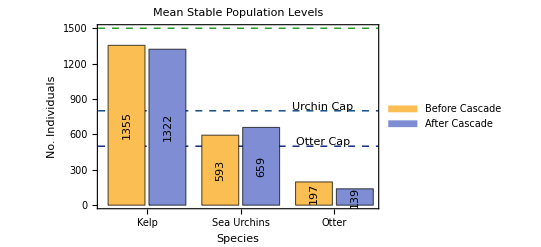

```mathematica
(* Plot effects of trophic cascade *)
lineAlg = Line[{{0.5, 1500}, {8, 1500}}]
lineSard = Line[{{0.5, 800}, {8, 800}}]
lineOtter = Line[{{0.5, 500}, {8, 500}}]

BarChart[
{{mAlgAfter, mAlgBefore},{mSardAfter, mSardBefore},{mSharkAfter, mSharkBefore}},ChartLabels->{{"Kelp","Sea Urchins", "Otter"},None}
,ChartLegends->{"Before Cascade","After Cascade"}, LegendAppearance->{-1, -1}, PlotLabel->"Mean Stable Population Levels"
,LabelingFunction->(Placed[Rotate[Round[#],0.5 Pi],If[#1>0.5,Center,Above]]&)
,Frame-> True
,FrameLabel->{"Species","No. Individuals"}
,PlotRange -> {Automatic,{0, 1500}}
,Prolog->
{
{Directive[{RGBColor[.11,.60,.11], Dashed}],lineAlg}, 
Style[Text["Algae Cap",{6,1535}], RGBColor[.3,.3,.3]],
{Directive[{RGBColor[.0,.25,.5], Dashed}],lineSard},
Style[Text["Urchin Cap",{6,835}], RGBColor[.3,.3,.3]],
{Directive[{RGBColor[.0,.1,.5], Dashed}],lineOtter},
Style[Text["Otter Cap",{6,535}], RGBColor[.3,.3,.3]]
}
]
```

```mathematica
(* Percentage changes in population composition *)
mAlgBefore / mAlgAfter* 1.
mSardBefore  / mSardAfter   * 1.
mSharkBefore  / mSharkAfter* 1.
```

0.975738

1.11072

0.704822

```mathematica
(* Load and example run data *)

exampleTCD = Import["cascade.dat", "Package"];
Length[exampleTCD[[1, 1]]]
```

1359

```mathematica
(* Load run data w/ moving average to reduce noise, 100-200 is a good number here *)
avgNo = 150;

maAlgae = MovingAverage[exampleTCD[[1, 1]], avgNo]; 
maSardines = MovingAverage[exampleTCD[[1, 2]], avgNo]; 
maSharks = MovingAverage[exampleTCD[[1, 3]], avgNo];

sardBirths = MovingAverage[exampleTCD[[2, 1]], avgNo];  
sardDeaths = MovingAverage[exampleTCD[[2, 3]], avgNo];
```

```mathematica
startOfCascadeAlg = Line[{{350, 0},{350, 1000 }}];
startOfCascadeSard = Line[{{350, 0},{350, 1000}}];
startOfCascadeShark = Line[{{350, 0},{350, 1000}}];

pAlg = ListLinePlot[
maAlgae
,PlotLabel-> "Kelp Population (MA of 150)"
,PlotStyle->RGBColor[.11,.60,.11]
,Frame->True
,FrameLabel->{"Time (No. Iterations)", "No. Individuals"}
, Filling->Axis
,Prolog-> 
{
{Directive[{RGBColor[.8, .4, .4],Dashed}], startOfCascadeAlg},
Style[Text["",{590, 500}], RGBColor[.4,.4,.4]]
}
];

pSard = ListLinePlot[
maSardines
,PlotLabel-> "Sea Urchin Population (MA of 150)"
,PlotStyle->RGBColor[.0,.25,.5]
,Frame->True
,FrameLabel->{"Time (No. Iterations)", "No. Individuals"}
,Prolog-> 
{
{Directive[{RGBColor[.8, .4, .4],Dashed}], startOfCascadeSard},
Style[Text["",{590, 75}], RGBColor[.4,.4,.4]]
}
, Filling->Axis];

pShark = ListLinePlot[
maSharks
,PlotLabel-> "Otter Population (MA of 150)"
,PlotStyle->RGBColor[.0,.1,.5]
,Frame->True
,FrameLabel->{"Time (No. Iterations)", "No. Individuals"}
,Prolog-> 
{
{Directive[{RGBColor[.8, .4, .4],Dashed}], startOfCascadeShark},
Style[Text["",{590, 10}], RGBColor[.4,.4,.4]]
}
, Filling->Axis];
```

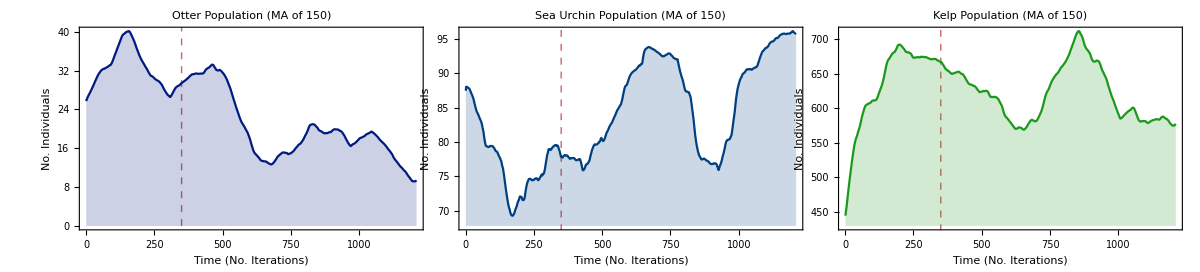

```mathematica
(* Compose plots in grid for printing*)
GraphicsGrid[{{ pShark, pSard, pAlg}}, Spacings->{-50,0}]
```

```mathematica
(* CLOC *)
$Line
```

123

## OVERFISHING

```mathematica
data["tSpawnRate"] = 5
```

5

```mathematica
checkExploitationRange[data, 10, 600, 1, True]
```

0

1

2

3

4

5

6

7

## HI THERE!!!

```mathematica
-Graphics-;
```

## I CAN SEE YOU!!!

```mathematica
EdgeDetect[CurrentImage[]]
```

-Graphics-